I am working through the guide Cloud Functions & Deployment. I mainly just go through Basic Examples.

```mathematica
CloudObject[]
```

CloudObject[https://www.wolframcloud.com/obj/f56bd5b4-efde-465f-b575-8c50e229c819]

```mathematica
CloudObject["/givenurl"]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/givenurl]

```mathematica
CloudObject["https://www.wolframcloud.com/obj/burbery1/givenurl1"]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/givenurl1]

```mathematica
URLRead[CloudObject["https://www.wolframcloud.com/obj/burbery1/givenurl1"]]
```

HTTPResponse[…]

```mathematica
CloudObject["/absolute/path"]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/absolute/path]

```mathematica
CloudObject["daily-summary"]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/daily-summary]

```mathematica
CloudPut[3^1000,CloudObject["big number"]]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/big number]

```mathematica
CloudGet[CloudObject["big number"]]
```

1322070819480806636890455259752144365965422032752148167664920368226828597346704899540778313850608061963909777696872582355950954582100618911865342725257953674027620225198320803878014774228964841274390400117588618041128947815623094438061566173054086674490506178125480344405547054397038895817465368254916136220830268563778582290228416398307887896918556404084898937609373242171846359938695516765018940588109060426089671438864102814350385648747165832010614366132173102768902855220001

```mathematica
DeleteObject[CloudObject["big number"]]
```

```mathematica
directory=CreateDirectory[CloudObject[]]
```

CloudObject[https://www.wolframcloud.com/obj/ef13570e-883d-4a3a-8b37-2fc7a86943d5]

```mathematica
CloudDeploy[Notebook[{Cell["Weekly Summary","Title"],Cell["Monday","Section"],Cell["Tuesday","Section"],Cell["Wednesday","Section"],Cell["Thursday","Section"],Cell[Friday,"Section"]}],FileNameJoin[{directory,"index.nb"}]]
```

CloudObject[https://www.wolframcloud.com/obj/ef13570e-883d-4a3a-8b37-2fc7a86943d5/index.nb]

```mathematica
cloudObject=CloudPut[Graphics3D[{Sphere[]}]]
```

CloudObject[https://www.wolframcloud.com/obj/9bdc521c-88ef-49a1-aa0e-037ad5d260c8]

```mathematica
CloudGet[cloudObject]
```

-Graphics3D-

```mathematica
CloudPut[Graphics3D[{Sphere[]}],"ball"]
```

CloudObject[https://www.wolframcloud.com/obj/burbery1/ball]

```mathematica
CloudGet["ball"]
```

-Graphics3D-

```mathematica
cc=CreateCloudExpression[Range[5]]
```

CloudExpression[…]

```mathematica
Get[cc]
```

{1,2,3,4,5}

```mathematica
AppendTo[cc,66]
```

CloudExpression[…]

```mathematica
Get[cc]
```

{1,2,3,4,5,66}

```mathematica
cc[[3]]=3
```

3

```mathematica
Get[cc]
```

{1,2,3,4,5,66}

```mathematica
cc[[2]]=.
```

```mathematica
Get[cc]
```

{1,3,4,5,66}

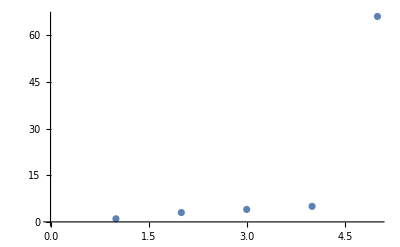

```mathematica
ListPlot[Get[cc]]
```

```mathematica
cc=CreateCloudExpression[Range[5],Permissions->"Public"]
```

CloudExpression[…]

```mathematica
cc=CreateCloudExpression[Range[5]]
```

CloudExpression[…]

```mathematica
Options[cc]
```

{Permissions→{Owner→{Read,Write,Execute}},PartProtection→Automatic}

```mathematica
SetPermissions[cc,"Public"]
```

{All→Automatic,Owner→{Read,Write,Execute}}

```mathematica
Options[cc]
```

{Permissions→{All→{Read},Owner→{Read,Write,Execute}},PartProtection→Automatic}

```mathematica
CloudDeploy[ExportForm[-Graphics-,"PNG"],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/d32bc71e-3a1a-4d84-8b75-b7e0bb1b6fe3]

```mathematica
CloudImport["https://wolframcloud.com/obj/d32bc71e-3a1a-4d84-8b75-b7e0bb1b6fe3"]
```

-Graphics-

```mathematica
Head[%]
```

Image

```mathematica
CloudShare["hannahburbery@wolfram.com"]
```

CloudObject[https://www.wolframcloud.com/obj/5760fbb8-3b66-48c4-a03c-ca52e6f95588]

```mathematica
CloudShare[{"hannahburbery@wolfram.com","timothyburbery@wolfram.com"}]
```

CloudDeploy::notauth: Unable to authenticate with Wolfram Cloud server. Please try authenticating again.

$Failed

```mathematica
CloudShare["burbery1@marshall.edu"]
```

CloudDeploy::notauth: Unable to authenticate with Wolfram Cloud server. Please try authenticating again.

$Failed

```mathematica
d
```